```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]


pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

(* 
https://blog.wolfram.com/2011/12/15/mathematica-qa-series-converting-to-conventional-mathematical-typesetting/
*)
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 276 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,VariationalMethods`,System`,Global`}

```mathematica
Clear[eq2pt1]
eq2pt1 = 
Subscript[p, 2]/Subscript[p, 1]== 1 + ((2 γ)/(γ+1)) ( Subscript[M, 1]^2 Sin[β]^2-1 )
```

p_2/p_1==1+(2 γ (-1+Sin[β]^2 M_1^2))/(1+γ)

```mathematica
Clear[eq2pt2]
eq2pt2 =  Subscript[p, 2]/Subscript[p, 1]== (2 γ)/(γ+1)Subscript[M, 1]^2 Sin[β]^2
```

p_2/p_1==(2 γ Sin[β]^2 M_1^2)/(1+γ)

```mathematica
Clear[eq2pt3]
eq2pt3 = 
Subscript[ρ, 2]/Subscript[ρ, 1]== (( γ + 1 ) Subscript[M, 1]^2 Sin[β]^2)/(( γ - 1 ) Subscript[M, 1]^2 Sin[β]^2+2)
```

ρ_2/ρ_1==((1+γ) Sin[β]^2 M_1^2)/(2+(-1+γ) Sin[β]^2 M_1^2)

```mathematica
Clear[eq2pt4]
eq2pt4 = eq2pt3[[1]] == 
Limit[ eq2pt3[[2]], Subscript[M, 1]-> ∞ ] // Simplify
```

(1+γ)/(-1+γ)==ρ_2/ρ_1

```mathematica
eq2pt2
eq2pt4
```

p_2/p_1==(2 γ Sin[β]^2 M_1^2)/(1+γ)

(1+γ)/(-1+γ)==ρ_2/ρ_1

```mathematica
Assuming[ Subscript[ρ, 2]/Subscript[ρ, 1] ≠ 0 , DivideSides[ eq2pt2, eq2pt4] ]
```

((-1+γ) p_2)/((1+γ) p_1)==(2 γ Sin[β]^2 M_1^2 ρ_1)/((1+γ) ρ_2)

```mathematica
Clear[eq2pt6]
eq2pt6 = 
Subscript[u, 2]/Subscript[V, 1]== 1 - (2 ( Subscript[M, 1]^2 Sin[β]^2-1 ))/((γ+1) Subscript[M, 1]^2)
```

u_2/V_1==1-(2 (-1+Sin[β]^2 M_1^2))/((1+γ) M_1^2)

```mathematica
Limit[ eq2pt6[[2]] , Subscript[M, 1]-> ∞ ]
```

(1+γ-2 Sin[β]^2)/(1+γ)

```mathematica
eq2pt7 = 
eq2pt6[[1]] == Limit[ eq2pt6[[2]] , Subscript[M, 1]-> ∞ ]
```

u_2/V_1==(1+γ-2 Sin[β]^2)/(1+γ)

```mathematica
Clear[eq2pt8]
eq2pt8 = 
Subscript[v, 2]/Subscript[V, 1]== (2 ( Subscript[M, 1]^2 Sin[β]^2 -1) Cot[β])/(( γ+1) Subscript[M, 1]^2)
```

v_2/V_1==(2 Cot[β] (-1+Sin[β]^2 M_1^2))/((1+γ) M_1^2)

```mathematica
Limit[ eq2pt8[[2]], Subscript[M, 1]-> ∞ ]  // Simplify
```

Sin[2 β]/(1+γ)

```mathematica
Clear[eq2pt10]
eq2pt10 = 
eq2pt8[[1]] == Limit[ eq2pt8[[2]], Subscript[M, 1]-> ∞ ]  // Simplify
```

v_2/V_1==Sin[2 β]/(1+γ)

```mathematica
Clear[eq2pt11]
eq2pt11 = 
Subscript[C, p]== (Subscript[p, 2]-Subscript[p, 1])/Subscript[q, 1]
```

C_p==(-p_1+p_2)/q_1

```mathematica
Subscript[q, 1]->γ/2 Subscript[p, 1] Subscript[M, 1]^2
```

q_1→1/2 γ M_1^2 p_1

```mathematica
Clear[eq2pt3a]
eq2pt3a = 
eq2pt11 /. Subscript[q, 1]->γ/2 Subscript[p, 1] Subscript[M, 1]^2 // Simplify
```

C_p==(2 (-p_1+p_2))/(γ M_1^2 p_1)

```mathematica
Clear[eq2pt13]
eq2pt13 = 
( Assuming[ Subscript[p, 1]≠ 0 , 
eq2pt3a /. Subscript[p, 2]->  P Subscript[p, 1] ] // Cancel  ) /. P -> (Subscript[p, 2]/Subscript[p, 1])
```

C_p==(2 (-1+p_2/p_1))/(γ M_1^2)

```mathematica
eq2pt13
eq2pt1
```

C_p==(2 (-1+p_2/p_1))/(γ M_1^2)

p_2/p_1==1+(2 γ (-1+Sin[β]^2 M_1^2))/(1+γ)

```mathematica
Clear[eq2pt14]
eq2pt14 = 
Assuming[ Subscript[M, 1]≠ 0 &&  γ ≠ 0 && γ+1 ≠ 0 , 
Eliminate[ { eq2pt13, eq2pt1 } , { Subscript[p, 2], Subscript[p, 1] } ] ][[1]]
```

C_p==(4 Sin[β]^2-4/M_1^2)/(1+γ)

```mathematica
Limit[ eq2pt14[[2]] , Subscript[M, 1]-> ∞ ]
```

(4 Sin[β]^2)/(1+γ)

```mathematica
Clear[eq2pt15]
eq2pt15 = 
Subscript[C, p]== Limit[ eq2pt14[[2]] , Subscript[M, 1]-> ∞ ]
```

C_p==(4 Sin[β]^2)/(1+γ)

```mathematica
Clear[eq2pt16]
eq2pt16 = 
Tan[θ] == 2 Cot[β] ((Subscript[M, 1]^2 Sin[β]^2-1)/(Subscript[M, 1]^2(γ+Cos[2 β])+2))
```

Tan[θ]==(2 Cot[β] (-1+Sin[β]^2 M_1^2))/(2+(γ+Cos[2 β]) M_1^2)

```mathematica
( eq2pt16[[1]] /. Tan[θ]-> Normal[Series[Tan[θ], { θ, 0, 1 } ]] )
```

θ

```mathematica
Clear[angleReplace]
angleReplace = 
{
Tan[θ]-> Normal[Series[Tan[θ], { θ, 0, 1 } ]] ,
Cot[β]-> Normal[Series[Cot[β], { β, 0, 0 } ]],
Sin[β]-> Normal[Series[Sin[β], { β, 0, 1 } ]] ,
Cos[2 β]-> Normal[Series[Cos[2 β], { β, 0, 1 }]] 
} ;
angleReplace // TableForm
```

Tan[θ]→θ
Cot[β]→1/β
Sin[β]→β
Cos[2 β]→1

```mathematica
eq2pt16 /. angleReplace
```

θ==(2 (-1+β^2 M_1^2))/(β (2+(1+γ) M_1^2))

```mathematica
Limit[
( eq2pt16 /. angleReplace ) , Subscript[M, 1]-> ∞ ]
```

lim_(M_1→∞) (θ==(2 (-1+β^2 M_1^2))/(β (2+(1+γ) M_1^2)))

```mathematica
Clear[eq2pt18]
eq2pt18 = 
Limit[ eq2pt16[[2]] /. angleReplace , Subscript[M, 1]-> ∞ ] // Simplify 
( Limit[ eq2pt16[[2]] /. angleReplace , Subscript[M, 1]-> ∞ ] // Simplify  ) /. γ-> 1.4
```

(2 β)/(1+γ)

0.833333 β

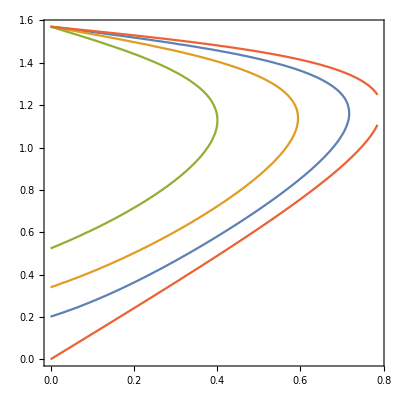

```mathematica
(* Page 37 *) 

ContourPlot[Evaluate[
{ 
( eq2pt16  /. { Subscript[M, 1]-> 5, γ-> 1.4 }  ),
( eq2pt16  /. { Subscript[M, 1]-> 3, γ-> 1.4 }  ),
( eq2pt16  /. { Subscript[M, 1]-> 2, γ-> 1.4 }  ) ,
( eq2pt16  /. { Subscript[M, 1]-> 100000, γ-> 1.4 }  )
}
] ,  { θ, 0, π/4} ,{ β, 0, π/2}]
```